```mathematica
ClearAll["Global`*"]
```

```mathematica
starvation =  ts*-Bm/(Em*Log[1-f0*M^(γ-1)]);
recovery = ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)]);
Ratio = FullSimplify[starvation/recovery]
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
Remove[starvation,M,B0,Bm,η,γ,f0,Em]
```

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
growth=RF[[1]];
starvation=RF[[2]];
mortality=RF[[3]];
recovery=RF[[4]];
maintenance=RF[[5]];
resourcegrowth=RF[[6]];
(*rhovalues = Table[x,{x,0.2,0.7,0.1}];*)
(*scalevalues = Table[x,{x,6,0.5,-0.6}];*)
(*sigmavalues =Table[x,{x,starvation/200,starvation/0.4,0.0000005}];*)
sigmavalues = RecurrenceTable[{B[n+1] == B[n]+1/50B[n],B[1]==2.3060191710825582*^-7},B,{n,1,325}];
ExtinctionSigma = ParallelTable[
Reps = 200;
ProportionExtinct=With[{
α=resourcegrowth,λ=growth,σ=sigma,ρ=recovery,β=maintenance,μ=mortality,T=100000000,threshold=10,PercentPerturbed=1.5},
ExtinctionReps = Table[
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0= (μ (-λ+σ))/(λ ρ+μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
(*F0=RandomReal[{1000,30000}];
H0 = RandomReal[{1000,30000}];
R0 = RandomReal[{1000,30000}];*)
(*Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ]*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
Rtraj = Flatten[Traj,1][[100;1000,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma/ρ,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigmavalues}(*,{rho,rhovalues}*)];
```

NDSolve::ndsz: At t == 44.2349, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.83795, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 7.27591×10^7; unable to continue.

NDSolve::ndsz: At t == 5.91309, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {72800000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {72800000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {72800000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.03006×10^7; unable to continue.

NDSolve::ndsz: At t == 4.86014×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 6.81015×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 8.01928×10^7; unable to continue.

NDSolve::ndsz: At t == 1.50415×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 495407., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 13.2903, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 7.03852×10^7; unable to continue.

NDSolve::ndsz: At t == 8.7765, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.33263×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 8.24362×10^7; unable to continue.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.88286×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 6.76425×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.94258×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 9.29169×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.69346, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 7.76663×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 6.89726×10^7; unable to continue.

NDSolve::ndsz: At t == 1.91157×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.33×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 658758., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {700000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 630274., step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 7.13031×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 7.29016×10^7; unable to continue.

NDSolve::ndsz: At t == 1.28235×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.18605×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 200001., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.74869, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.52729, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.18768×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.41183×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 5.54707×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.05446×10^7; unable to continue.

InterpolatingFunction::dmval: Input value {60600000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.79974, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.30469, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.66003, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.21429×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 4.53442×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.15711, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.95289, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 3.92366×10^7; unable to continue.

NDSolve::ndsz: At t == 4.47371, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 4.78547×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 4.00925×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.40056, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.81645×10^7; unable to continue.

NDSolve::ndsz: At t == 6.06436, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 3.59903×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 3.43509×10^7; unable to continue.

NDSolve::ndsz: At t == 2.92271, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 9.28962, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.5185, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.93116, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 2.81271×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 2.76472×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 2.91564×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.60121, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.31907, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.98347×10^7; unable to continue.

NDSolve::ndsz: At t == 2.92734, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 4.60723×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 4.21709×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.96945, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.29732, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.89961, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 2.35668×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 2.29017×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 2.22716×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 3.29131×10^7; unable to continue.

InterpolatingFunction::dmval: Input value {33000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.30571, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.82339×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 1.9908×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.5819, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.35004, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 9.89357, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nderr: Error test failure at t == 1.04056×10^7; unable to continue.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 2.66412, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10500000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nderr: Error test failure at t == 1.47292×10^7; unable to continue.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 2.28522×10^7; unable to continue.

NDSolve::ndsz: At t == 2.90554, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.37516×10^7; unable to continue.

NDSolve::ndsz: At t == 3.43099, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 2.479×10^7; unable to continue.

NDSolve::ndsz: At t == 4.39334, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.64495×10^7; unable to continue.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.14748, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.5697×10^6; unable to continue.

InterpolatingFunction::dmval: Input value {9600000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 12.8916, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.39263×10^7; unable to continue.

NDSolve::ndsz: At t == 1.29146×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.93941, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 1.32901×10^7; unable to continue.

General::stop: Further output of NDSolve :: nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.05689×10^7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {20600000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.21313, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.52531×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 9.37251×10^6, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {9400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.08282, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.59128, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.47835, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.43989×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.53354, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.53001, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.133×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.05722×10^7, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 1.11528×10^7. Unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 1.27632×10^7. Unable to continue.

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat",ExtinctionSigma]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat

```mathematica
ExtinctionSigma=ToExpression[Import["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat","Data"]];
```

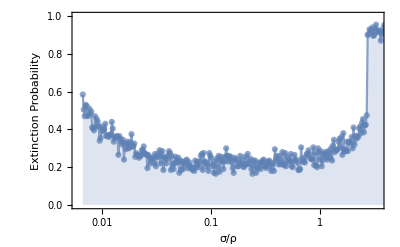

```mathematica
ExtinctionsAllometricPlot=Show[{
ListLogLinearPlot[ExtinctionSigma,PlotRange->{{0.006,3.4},{0,1}},PlotStyle->Directive[Opacity[0.7]],Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListLogLinearPlot[ExtinctionSigma,PlotRange->{0,1},Joined->True,Filling->Bottom,PlotStyle->Directive[Opacity[0.7]]](*,
step=10;If[EvenQ[step],step=step+1];
ListLogLinearPlot[
MovingAverage[
Re[ExtinctionSigma],step],PlotStyle->ColorData[97,8],Joined->True(*Transpose[{Re[ExtinctionSigma[[1+IntegerPart[N[step/2]];;Length[ExtinctionSigma]-IntegerPart[N[step/2]],1]]],MovingAverage[ExtinctionSigma[[All,2]],step]}],PlotStyle->ColorData[97,8],Joined->True*)
]*)
},ImageSize->400]
```

```mathematica
RatioValues=(
noise=0.4;
ParallelTable[
value=Re[Ratio/.{
M->10^2,
η->3/4,
γ->1.19,
f0->0.0202*(1+RandomReal[{-noise,noise}]),
B0->1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
Bm->0.0245*(1+RandomReal[{-noise,noise}])
}];
{value,i},
{i,0.1,10,0.001}]
);
```

```mathematica
RatioValuePlot=ListLogLinearPlot[RatioValues,PlotRange->{{0.006,3.4},All},FrameTicks->None,Frame->True,AspectRatio->1/10,PlotStyle->Directive[{Opacity[0.05]}]]
```

-Graphics-

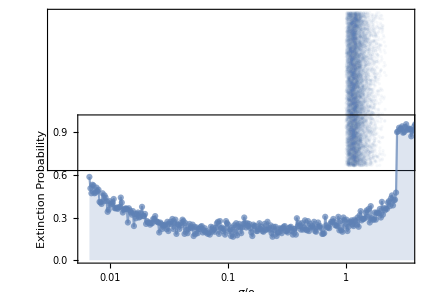

```mathematica
CombinedAllometricPlot=GraphicsColumn[{
Show[RatioValuePlot,ImagePadding->{{43,14},{Automatic,Automatic}}],
Show[
ExtinctionsAllometricPlot,ImagePadding->{{40,10},{Automatic,Automatic}}]},Spacings->Scaled[-0.65],ImagePadding->{{0,0},{110,40}}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf",CombinedAllometricPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat",ExtinctionSigma]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctionSigmaRhoAllometry.dat